## Base model - analytic

```mathematica
Lambda[rh_,mh_,re_,me_]:=1/2 (re+rh-me-mh+√((-re-rh+me+mh)^2-4 (re rh-re me-rh mh)))
```

```mathematica
DLDre[rh_,mh_,re_,me_]:=1/4 (2+(2 (me-mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
DLDrh[rh_,mh_,re_,me_]:=1/4 (2-(2 (me-mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
DLDmh[rh_,mh_,re_,me_]:=1/4 (-2+(2 (me+mh-re+rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
DLDme[rh_,mh_,re_,me_]:=1/4 (-2+(2 (me+mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
Solve[-DLDmh[rho,m,1,m]==DLDrh[rho,m,1,m],m]
```

{{m→1-rho}}

## Base model + global competition

```mathematica
eq1={D[nH[t],t]==rh*nH[t]-me*nH[t]+mh*nE[t]-k*(nH[t])^2,nH[0]==nH0}
```

{nH'[t]==mh nE[t]-me nH[t]+rh nH[t]-k nH[t]^2,nH[0]==nH0}

```mathematica
eq2={D[nE[t],t]==me*nH[t]+(re-mh)nE[t],nE[0]==nE0}
```

{nE'[t]==(-mh+re) nE[t]+me nH[t],nE[0]==nE0}

```mathematica
sys={eq1,eq2}
```

{{nH'[t]==mh nE[t]-me nH[t]+rh nH[t]-k nH[t]^2,nH[0]==nH0},{nE'[t]==(-mh+re) nE[t]+me nH[t],nE[0]==nE0}}

```mathematica
Biglambda[tmax_,nh0_,ne0_,nhf_,nef_]:=(1/tmax)*Log[(nhf+nef)/(nh0+ne0)];
```

## Functions definition

```mathematica
(*Function that takes all the Rempl parameters as arguments and returns a table of same format containing the final values of the numerical solution of the system of equations:*)
```

```mathematica
SolutionCalc[Rempl_,nE0t_,nH0t_]:=(Module[{tabT,TabRHO,TabM,TabK},
tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;Table[{nE[tabT[[itmax]]],nH[tabT[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->nE0t/.nH0->nH0t,{nE,nH},{t,0,tabT[[itmax]]}],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}]])
```

```mathematica
(*Function that takes all the Rempl parameters AND the solution as arguments and returns the lambda values in a table of same format as Rempl*)
```

```mathematica
LambdaCalc[Rempl_,Solu_,nE0t_,nH0t_]:=(Module[{tabT,TabRHO,TabM,TabK},
tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;
Table[Biglambda[tabT[[itmax]], nH0t,nE0t,Solu⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,Solu⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}]])
```

```mathematica
(*Function that takes as argument the parameters Rempl and returns a list of {the solution, the corresponding lambda, sensi1,sensi2,sensi3,...}*)
```

```mathematica
SensitivityCalc[Rempl_,nE0t_,nH0t_,α_]:=(Module[{tabT,RE,TabRHO,TabM,TabK,Solu,DTabRHO,DTabM,DRHRempl,DMERempl,DMHRempl,DRHSol,DMESol,DMHSol,Lambda,DRHLambda,DMELambda,DMHLambda,SensiRH,SensiRE,SensiMH,SensiME,SensiK,TabRHdim,TabMdim},

tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;
RE = Rempl⟦1,;;,1,1,2⟧[[1,2]];

TabRHdim=Table[TabRHO[[irho]],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];
TabMdim=Table[TabM[[im]],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];

Solu = SolutionCalc[Rempl,nE0t,nH0t];

DTabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧+α;
DTabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧+α;

DRHRempl =Table[{tmax->tabT⟦itmax⟧,re->RE,rh-> DTabRHO⟦irho⟧,me->TabM⟦im⟧,mh->TabM⟦im⟧,k->TabK⟦ik⟧},{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];
DMERempl = Table[{tmax->tabT⟦itmax⟧,re->RE,rh-> TabRHO⟦irho⟧,me->DTabM⟦im⟧,mh->TabM⟦im⟧,k->TabK⟦ik⟧},{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];
DMHRempl = Table[{tmax->tabT⟦itmax⟧,re->RE,rh-> TabRHO⟦irho⟧,me->TabM⟦im⟧,mh->DTabM⟦im⟧,k->TabK⟦ik⟧},{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];

DRHSol = SolutionCalc[DRHRempl,nE0t,nH0t];
DMESol = SolutionCalc[DMERempl,nE0t,nH0t];
DMHSol = SolutionCalc[DMHRempl,nE0t,nH0t];

Lambda = LambdaCalc[Rempl,Solu,nE0t,nH0t];
DRHLambda = LambdaCalc[DRHRempl,DRHSol,nE0t,nH0t];
DMELambda = LambdaCalc[DMERempl,DMESol,nE0t,nH0t];
DMHLambda = LambdaCalc[DMHRempl,DMHSol,nE0t,nH0t];

SensiRH =(1/α)*(DRHLambda-Lambda);
SensiME =(1/α)*(DMELambda-Lambda);
SensiMH =(1/α)*(DMHLambda-Lambda);

{Solu,Lambda,SensiRH,SensiME,SensiMH}]

)
```

```mathematica
(*Function that takes Rempl as an argument and returns {Sensitivities (format of the previous function),Optimal strategies (of same format as Rempl)}.*)
```

```mathematica
OptimalStrategy[Rempl_,nE0t_,nH0t_,α_]:=(Module[{tabT,TabRHO,TabM,TabK,RE,Sensitivities,SensiRH,SensiME,SensiMH,Opt},
tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;
RE = Rempl⟦1,;;,1,1,2⟧[[1,2]];

Sensitivities = SensitivityCalc[Rempl,nE0t,nH0t,α];
SensiRH = Sensitivities[[3]];
SensiME = Sensitivities[[4]];
SensiMH = Sensitivities[[5]];

Opt=Table[Sign[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}⟦Position[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}],Max[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}]]]⟦1,1⟧⟧]*Position[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}],Max[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}]]]⟦1,1⟧,{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];

{Sensitivities,Opt}])
```

### Equilibrium

```mathematica
eq1U=0==rE*nE-mH*nE+mE*nH
```

0==-mH nE+mE nH+nE rE

```mathematica
eq2U=0==rH*nH-mE*nH+mH*nE-k*nH*nH
```

0==mH nE-mE nH-k nH^2+nH rH

```mathematica
sysU={eq1U,eq2U}
```

{0==-mH nE+mE nH+nE rE,0==mH nE-mE nH-k nH^2+nH rH}

```mathematica
SolU=FullSimplify[Solve[sysU,{nE,nH}]]
```

{{nE→0,nH→0},{nE→(mE (mE rE+(mH-rE) rH))/(k (mH-rE)^2),nH→((mE rE)/(mH-rE)+rH)/k}}

```mathematica
(*Diverges in mh=re=1*)
```

```mathematica
nEU[rE_,rH_,mE_,mH_]:=(mE (mE rE+(mH-rE) rH))/(k (mH-rE)^2)
```

```mathematica
nHU[rE_,rH_,mE_,mH_]:=((mE rE)/(mH-rE)+rH)/k
```

```mathematica
nEU[1,rh,m,m]
```

(m (m+(-1+m) rh))/(k (-1+m)^2)

```mathematica
nHU[1,rh,m,m]
```

(m/(-1+m)+rh)/k

```mathematica
FullSimplify[Sign[Assuming[m>1&&k>0&&rho>-1,nHU[rho,m]]]]
```

Sign[nHU[rho,m]]

```mathematica
(*It is actually easy to look at the sign of those equilibria analytically (and also to calculate them). First of all, we have nEU=-(m/(1-m))nHU. Which means, since we only consider positive m, that if we want both of them to be positive at the same time then we need m>1. Then we can look at the positivity of just nHU. Since k is positive we find that nHU is positive if m+rho(m-1)>0 ie m>rho/(1+rho). Let us look at  *)
```

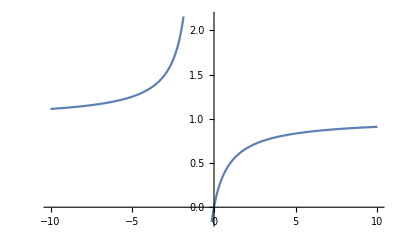

```mathematica
Plot[rho/(1+rho),{rho,-10,10}]
```

```mathematica
(*For the region of the parameter space we are interested in (rho>-1) the condition m>1 is thus sufficient for the existence of a positive equilibrium. Intuitively it makes sense: if migration is so important that microbes migrate out of the environment faster than they replicate in it (m>rE) then the exponential growth never truly has the time to kick in and competition is efficient everywhere despite formally existing only in the host. If migration is smaller than replication though, we DO have dnE/dt always positive, and a population that explodes in the environment. Let us check with some dynamics below*)
```

```mathematica
finalPop[re_,rh_,me_,mh_]:=nEU[re,rh,me,mh]+nHU[re,rh,me,mh]
```

```mathematica
D[finalPop[re,rh,me,mh],rh]
```

1/k+me/(k (mh-re))

```mathematica
FullSimplify[D[finalPop[re,rh,me,mh],rh]/.re->1/.me->m/.mh->m]
```

(2+1/(-1+m))/k

```mathematica
DLDRHO[rho_,m_]:=(2+1/(-1+m))/k
```

```mathematica
FullSimplify[D[finalPop[re,rh,me,mh],mh]/.re->1/.me->m/.mh->m]
```

(m (1+rh-m (3+rh)))/(k (-1+m)^3)

```mathematica
DLDM[rh_,m_]:=(m (1+rh-m (3+rh)))/(k (-1+m)^3)
```

```mathematica
Sol=Refine[Solve[DLDM[rho,m]==-DLDRHO[rho,m],m],m>0&&rho<1&&rho>-1]
```

{{m→(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3)},{m→(8+rho)/6+((1+ⅈ √3) (-34-10 rho-rho^2))/(12 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))-1/12 (1-ⅈ √3) (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3)},{m→(8+rho)/6+((1-ⅈ √3) (-34-10 rho-rho^2))/(12 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))-1/12 (1+ⅈ √3) (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3)}}

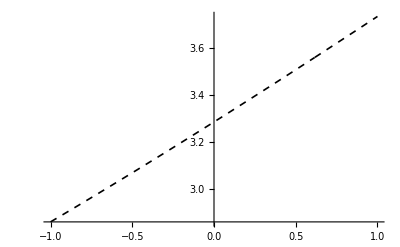

```mathematica
Plot[{(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3)},{rho,-1,1},PlotStyle->{Directive[Black,Thickness[0.003],Dashed]},PlotRange->All]
```

## Figure 3 panel C

```mathematica
tmaxB = {30};
NE0 =1;
NH0 = 0;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Flatten[{Table[i,{i,0,0.1,0.01}],Table[i,{i,0.15,4,0.05}]}];
TabKH =10^-{10,9,8,7,6,5,4,3,2,1};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatA=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

### Optimal strategies

```mathematica
OptTest=ResultatA[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{{{{-1.,0.,-3},{-1.,0.01,-3},{-1.,0.02,-3},{-1.,0.03,-3},{-1.,0.04,-3},{-1.,0.05,-3},{-1.,0.06,-3},{-1.,0.07,-3},{-1.,0.08,-3},{-1.,0.09,-3},{-1.,0.1,-3},{-1.,0.15,-3},{-1.,0.2,-3},3623,{1.,3.4,1},{1.,3.45,1},{1.,3.5,1},{1.,3.55,1},{1.,3.6,1},{1.,3.65,1},{1.,3.7,1},{1.,3.75,1},{1.,3.8,1},{1.,3.85,1},{1.,3.9,1},{1.,3.95,1},{1.,4.,1}}},8,{{1}}}
 |  |  |  |

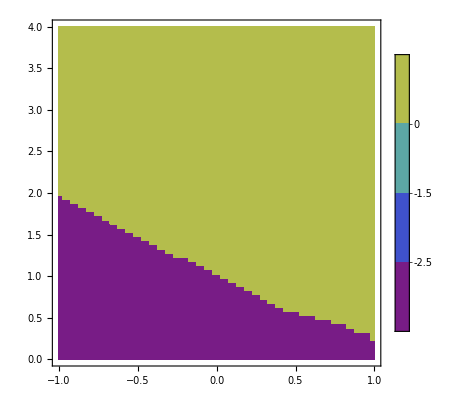
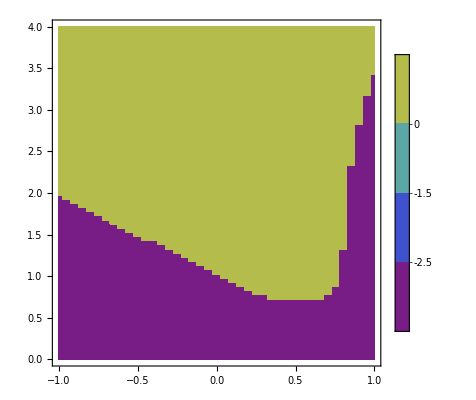
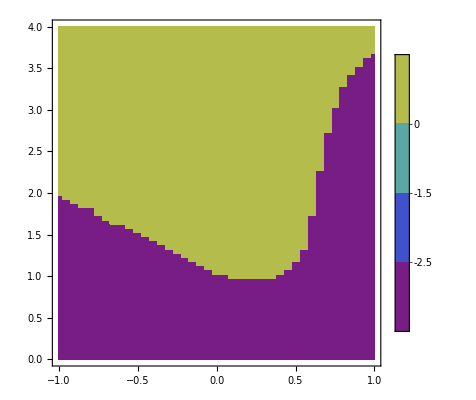
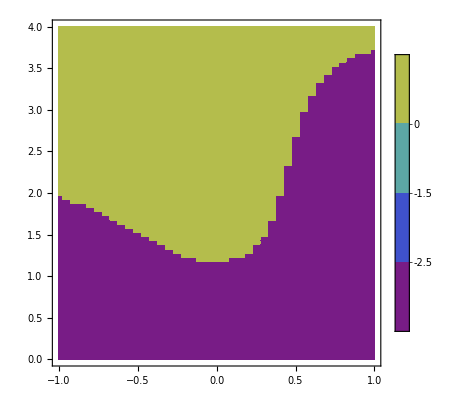
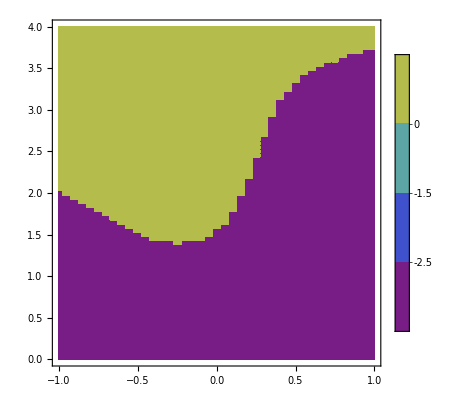
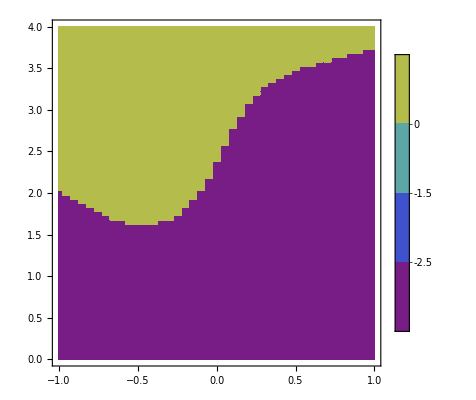
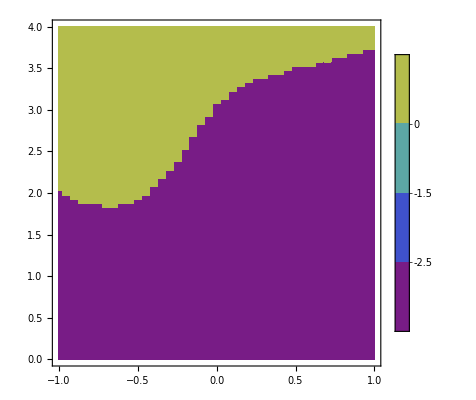
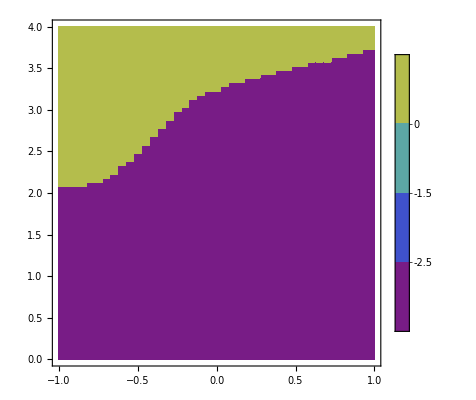

```mathematica
Table[ListContourPlot[dataOptTest⟦ik,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{ik,1,Length[TabKH]}]
```

## ContourPlot

```mathematica
listcolor=Reverse[Table[ColorData["SolarColors"][k],{k,0,1,1/(Length[TabKH]-1)}]]
```

{RGBColor[1., 0.820127, 0.126955],RGBColor[1., 0.7431501111111112, 0.10616206666666668],RGBColor[1., 0.6661732222222222, 0.08536913333333333],RGBColor[0.9899876666666667, 0.5566463333333334, 0.06420996666666667],RGBColor[0.9766378888888889, 0.43626944444444443, 0.04292872222222222],RGBColor[0.937111, 0.3196685555555555, 0.02599205555555556],RGBColor[0.871407, 0.20684366666666665, 0.013399966666666667],RGBColor[0.7828637777777778, 0.10864444444444443, 0.0052745333333333345],RGBColor[0.6258028888888889, 0.054322222222222216, 0.010549066666666667],RGBColor[0.468742, 0., 0.0158236]}

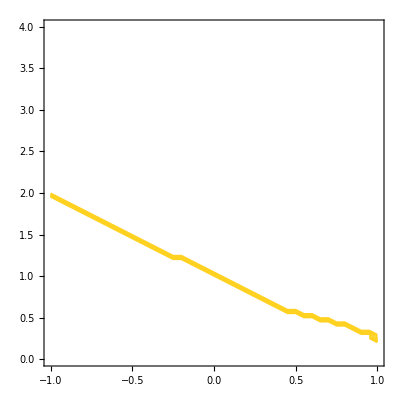
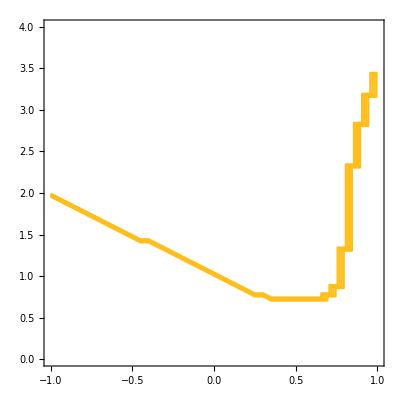
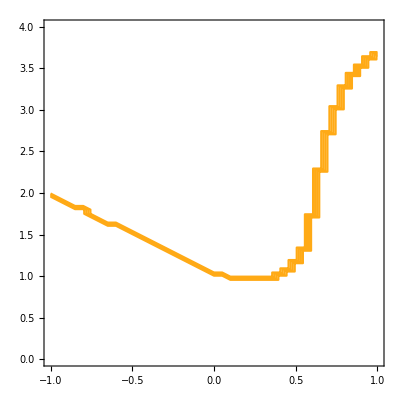
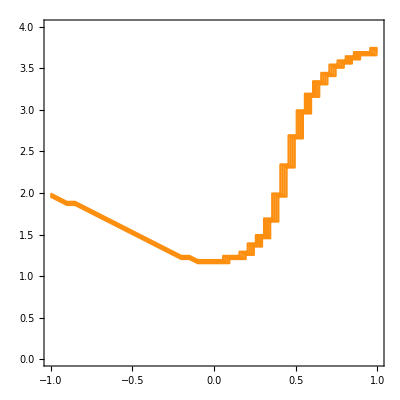
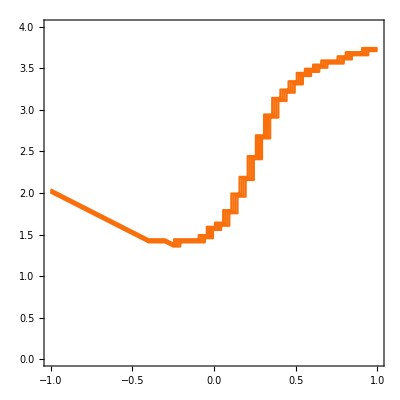
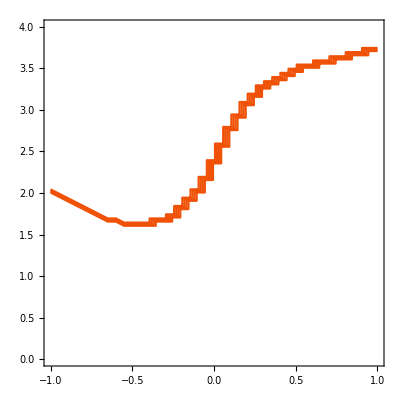
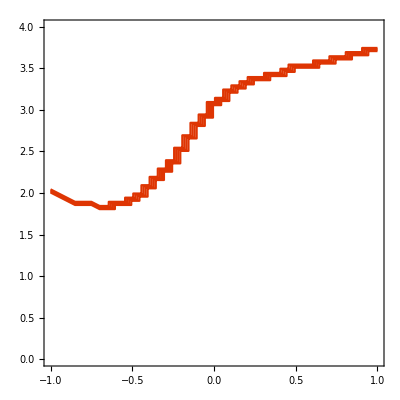
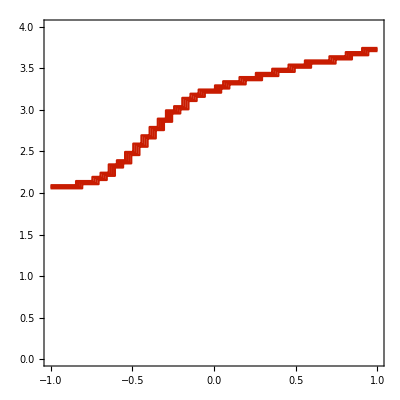

```mathematica
Table[ListContourPlot[dataOptTest[[ik,1]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{ik,1,Length[TabKH]}]
```

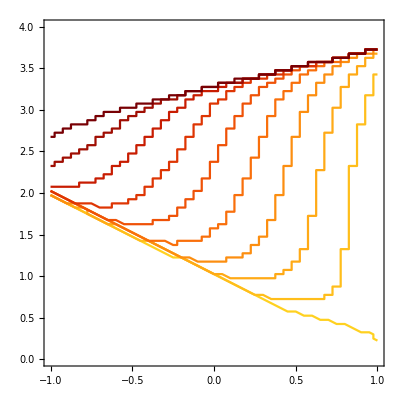

```mathematica
Show[Table[ListContourPlot[dataOptTest[[ik,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{ik,1,Length[TabKH]}]]
```

```mathematica
SensiRH=ResultatA[[1,3]];
```

```mathematica
SensiMH=ResultatA[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiRH[[itmax]][[irho]][[im]][[ik]]/SensiMH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

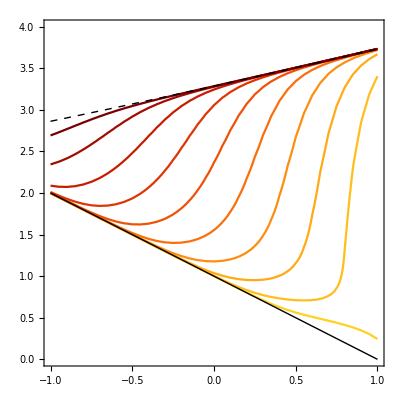

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[ik,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{ik,1,Length[TabKH]}],Plot[(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thick,Dashed]],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]]
```

## Extract some Lambda parametric maps (fugure 3 panel A)

```mathematica
Lambda=ResultatA[[1,2]];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],Lambda[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

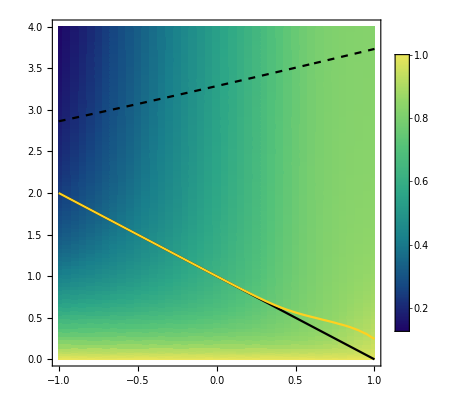

```mathematica
Show[ListDensityPlot[dataLambda⟦1,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.12,1}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16}],Plot[(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thick,Dashed]],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],ListContourPlot[dataSensiRatio[[1,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[1]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

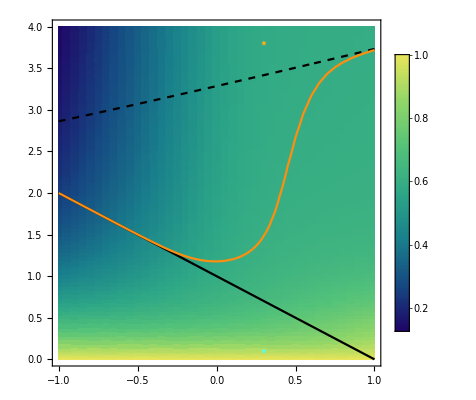

```mathematica
Show[ListDensityPlot[dataLambda⟦4,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.12,1}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16}],Plot[(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3),{rho,-1,1},PlotStyle->Directive[Dashed,Black,Thick]],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],ListContourPlot[dataSensiRatio[[4,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[4]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],ListPlot[{{0.3,3.8}},PlotMarkers->{Style[★,Large,RGBColor[1., 0.68, 0.1]]},PlotStyle->PointSize[Large]],ListPlot[{{0.3,0.1}},PlotMarkers->{Style[★,Large,RGBColor[0.33, 1., 0.92]]},PlotStyle->PointSize[Large]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

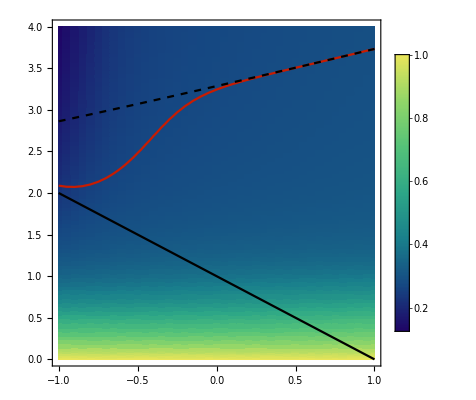

```mathematica
Show[ListDensityPlot[dataLambda⟦8,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.12,1}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],ListContourPlot[dataSensiRatio[[8,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[8]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],Plot[(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thick,Dashed]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

## Temporal plots - figure 3 panel B

```mathematica
Solu1 = NDSolve[sys/.{re->1,rh-> 0.3,me->0.1,mh->0.1,k->10^-7,nH0->0,nE0->1},{nE,nH},{t,0,100},MaxStepSize->0.0001]
```

{{nE→InterpolatingFunction[{{0., 100.}}, <>],nH→InterpolatingFunction[{{0., 100.}}, <>]}}

```mathematica
Solu2= NDSolve[sys/.{re->1,rh-> 0.3,me->3.8,mh->3.8,k->10^-7,nH0->0,nE0->1},{nE,nH},{t,0,100},MaxStepSize->0.0001]
```

{{nE→InterpolatingFunction[{{0., 100.}}, <>],nH→InterpolatingFunction[{{0., 100.}}, <>]}}

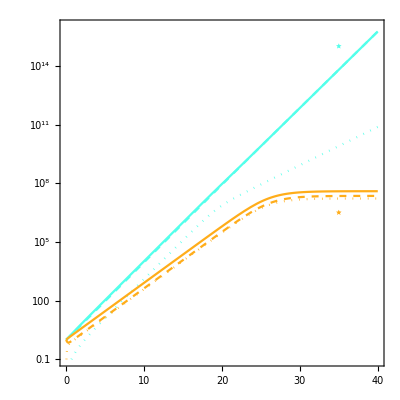

```mathematica
Show[LogPlot[{(nE[t]+nH[t])/.Solu1,(nE[t])/.Solu1,(nH[t])/.Solu1,(nE[t]+nH[t])/.Solu2,(nE[t])/.Solu2,(nH[t])/.Solu2},{t,0,40},Frame->True,PlotStyle->{RGBColor[0.33, 1., 0.92],Directive[RGBColor[0.33, 1., 0.92],Dashed],Directive[Dotted,RGBColor[0.33, 1., 0.92]],RGBColor[1., 0.68, 0.1],Directive[Dashed,RGBColor[1., 0.68, 0.1]],Directive[RGBColor[1., 0.68, 0.1],Dotted]},PlotRange->{All,{10^-1,10^16}},AspectRatio->1,LabelStyle->{FontSize->18,FontFamily->"Arial",Black},FrameTicks->{{{{10^0,"10^0"},{10^3,"10^3"},{10^6,"10^6"},{10^9,"10^9"},{10^12,"10^12"},{10^15,"10^15"}},None},{Automatic,None}}],ListLogPlot[{{35,10^6.5}},PlotMarkers->{Style[★,Large,RGBColor[1., 0.68, 0.1]]},PlotStyle->PointSize[Large]],ListLogPlot[{{35,10^15}},PlotMarkers->{Style[★,Large,RGBColor[0.33, 1., 0.92]]},PlotStyle->PointSize[Large]]]
```

## Supplementary 3, panel A

```mathematica
tmaxB = {30};
NE0 =0;
NH0 = 1;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Flatten[{Table[i,{i,0,0.1,0.01}],Table[i,{i,0.15,4,0.05}]}];
TabKH =10^-{10,9,8,7,6,5,4,3,2,1};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatB=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

### Optimal strategies

```mathematica
OptTest=ResultatB[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{{{{-1.,0.,2},{-1.,0.01,2},{-1.,0.02,2},{-1.,0.03,2},{-1.,0.04,-3},{-1.,0.05,-3},{-1.,0.06,-3},{-1.,0.07,-3},{-1.,0.08,-3},{-1.,0.09,-3},{-1.,0.1,-3},{-1.,0.15,-3},{-1.,0.2,-3},{-1.,0.25,-3},3622,{1.,3.4,1},{1.,3.45,1},{1.,3.5,1},{1.,3.55,1},{1.,3.6,1},{1.,3.65,1},{1.,3.7,1},{1.,3.75,1},{1.,3.8,1},{1.,3.85,1},{1.,3.9,1},{1.,3.95,1},{1.,4.,1}}},9}
 |  |  |  |

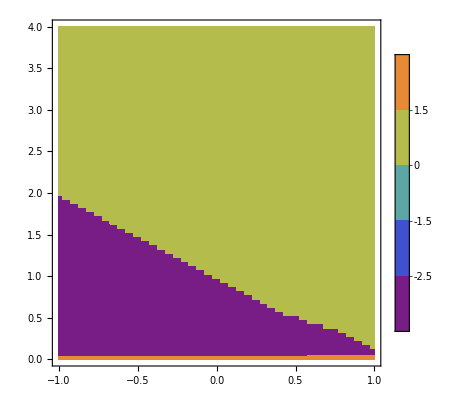
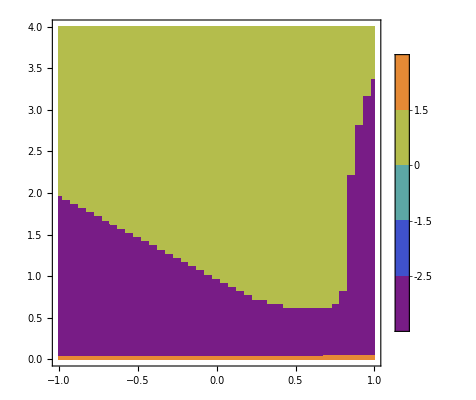
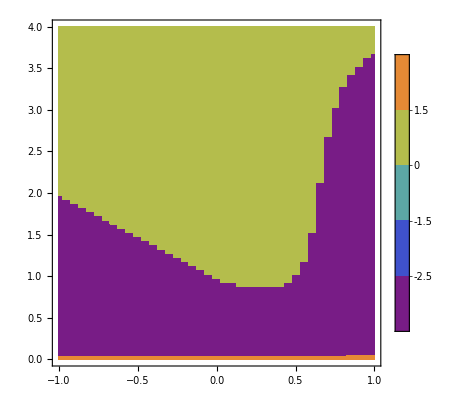
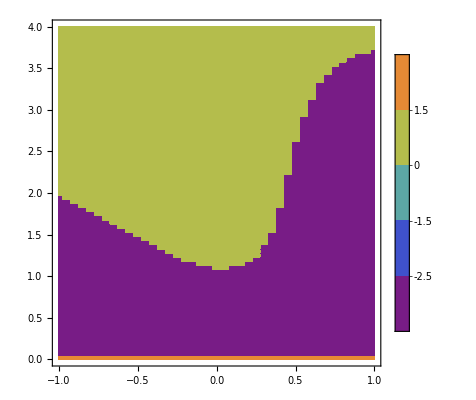
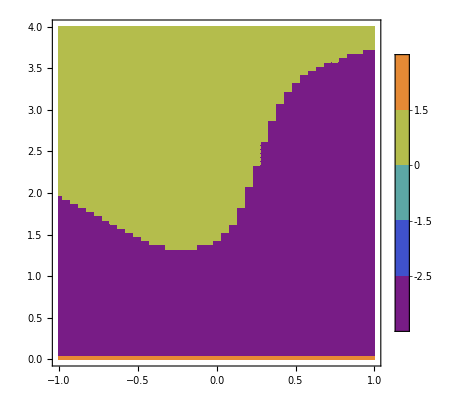
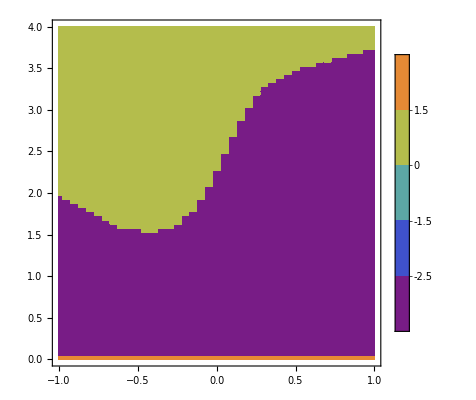
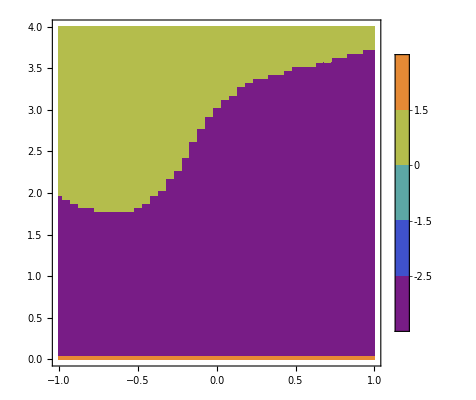
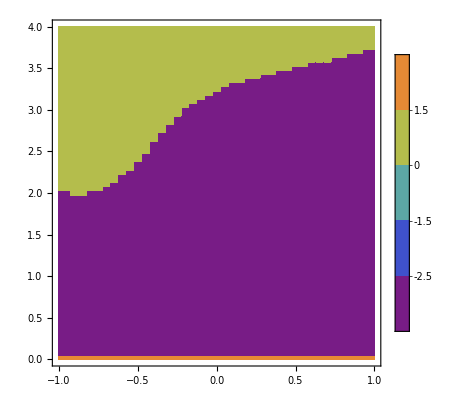

```mathematica
Table[ListContourPlot[dataOptTest⟦ik,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{ik,1,Length[TabKH]}]
```

## ContourPlot

```mathematica
listcolor=Reverse[Table[ColorData["SolarColors"][k],{k,0,1,1/(Length[TabKH]-1)}]]
```

{RGBColor[1., 0.820127, 0.126955],RGBColor[1., 0.7431501111111112, 0.10616206666666668],RGBColor[1., 0.6661732222222222, 0.08536913333333333],RGBColor[0.9899876666666667, 0.5566463333333334, 0.06420996666666667],RGBColor[0.9766378888888889, 0.43626944444444443, 0.04292872222222222],RGBColor[0.937111, 0.3196685555555555, 0.02599205555555556],RGBColor[0.871407, 0.20684366666666665, 0.013399966666666667],RGBColor[0.7828637777777778, 0.10864444444444443, 0.0052745333333333345],RGBColor[0.6258028888888889, 0.054322222222222216, 0.010549066666666667],RGBColor[0.468742, 0., 0.0158236]}

```mathematica
{RGBColor[1., 0.820127, 0.126955],RGBColor[1., 0.7431501111111112, 0.10616206666666668],RGBColor[1., 0.6661732222222222, 0.08536913333333333],RGBColor[0.9899876666666667, 0.5566463333333334, 0.06420996666666667],RGBColor[0.9766378888888889, 0.43626944444444443, 0.04292872222222222],RGBColor[0.937111, 0.3196685555555555, 0.02599205555555556],RGBColor[0.871407, 0.20684366666666665, 0.013399966666666667],RGBColor[0.7828637777777778, 0.10864444444444443, 0.0052745333333333345],RGBColor[0.6258028888888889, 0.054322222222222216, 0.010549066666666667],RGBColor[0.468742, 0., 0.0158236]}
```

```mathematica
SensiRH=ResultatB[[1,3]];
```

```mathematica
SensiMH=ResultatB[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiMH[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

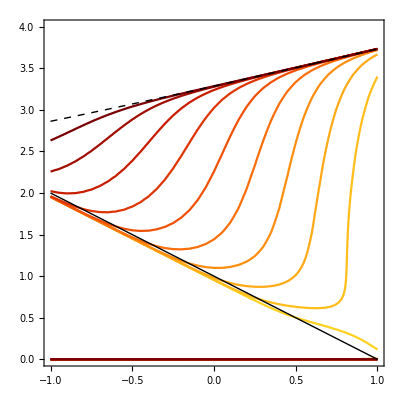

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[ik,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{ik,1,Length[TabKH]}],Plot[(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thick,Dashed]],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

## Supplementary figure 3 - panel B

```mathematica
tmaxB = {20,25,30,35,40,50,60};
NE0 =1;
NH0 = 0;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Flatten[{Table[i,{i,0,0.1,0.01}],Table[i,{i,0.15,4,0.07}]}];
TabKH =10^-{7};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatC=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

### Optimal strategies

```mathematica
OptTest=ResultatC[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{{1}}
 |  |  |  |

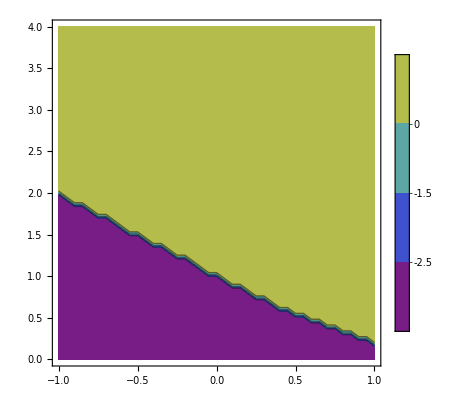
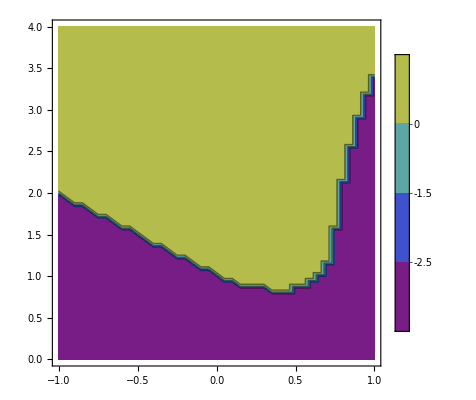
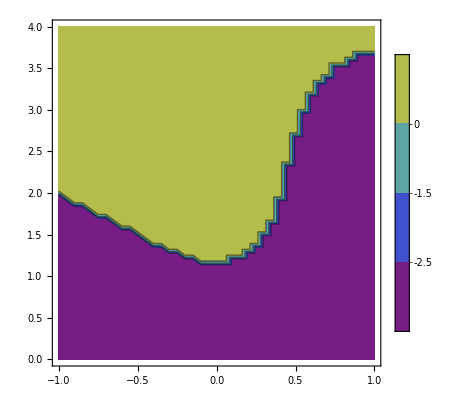
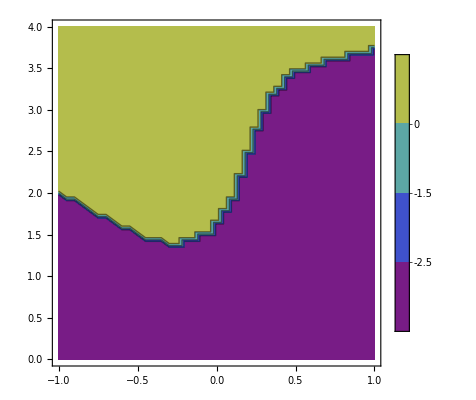
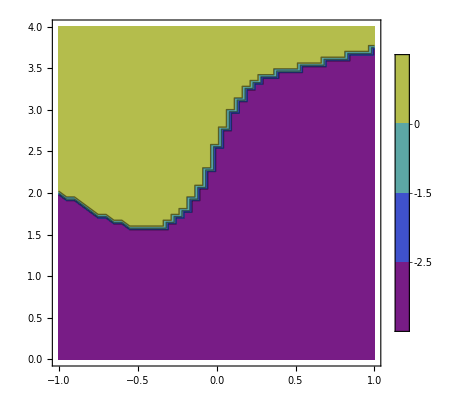
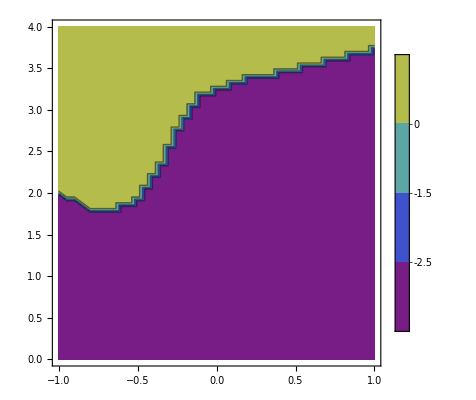
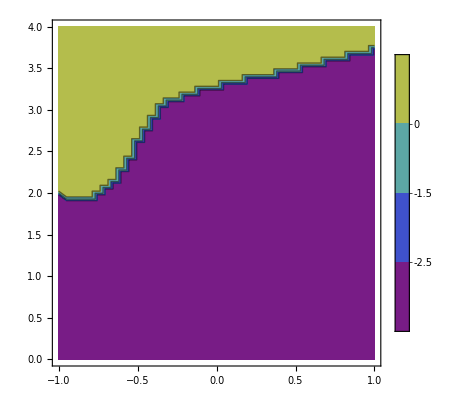

```mathematica
Table[ListContourPlot[dataOptTest⟦1,itmax⟧,Mesh->None,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

### Contour Plot

```mathematica
listcolor=Reverse[Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[tmaxB]-1)}]]
```

{RGBColor[0.914809, 0.897673, 0.350652],RGBColor[0.571909, 0.839991, 0.408102],RGBColor[0.329526, 0.762208, 0.474596],RGBColor[0.175507, 0.652273, 0.528496],RGBColor[0.097699, 0.498132, 0.548165],RGBColor[0.0839935, 0.279645, 0.510102],RGBColor[0.122103, 0.00901808, 0.39826]}

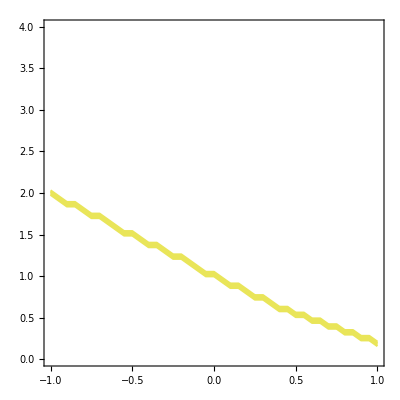
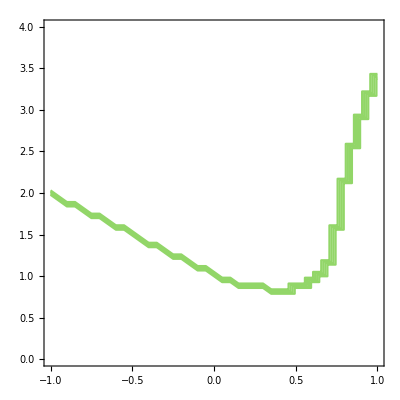
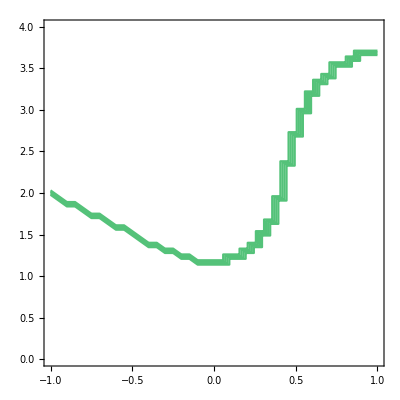
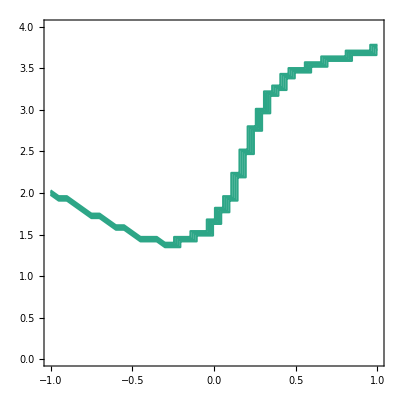
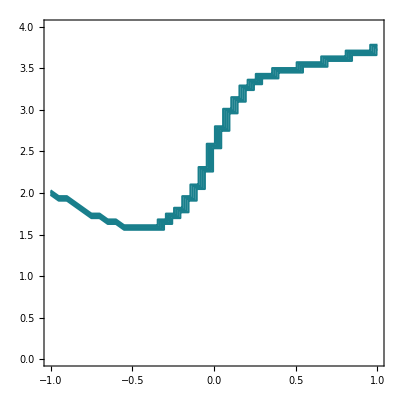
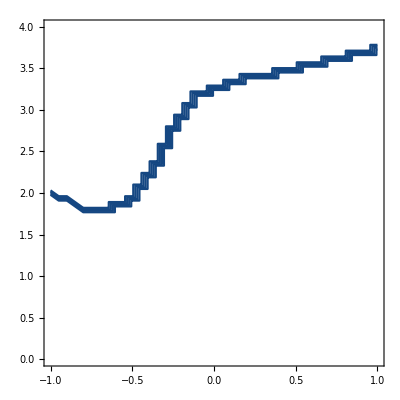
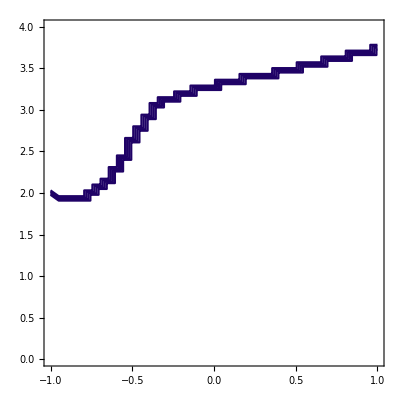

```mathematica
Table[ListContourPlot[dataOptTest[[1,itmax]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}]
```

```mathematica
SensiRH=ResultatC[[1,3]];
```

```mathematica
SensiMH=ResultatC[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiRH[[itmax]][[irho]][[im]][[ik]]/SensiMH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

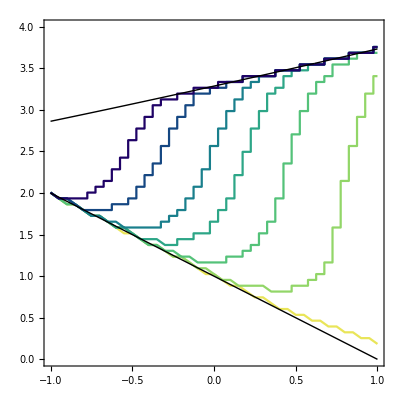

```mathematica
Show[Table[ListContourPlot[dataOptTest[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}],Plot[(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thick]],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]]
```

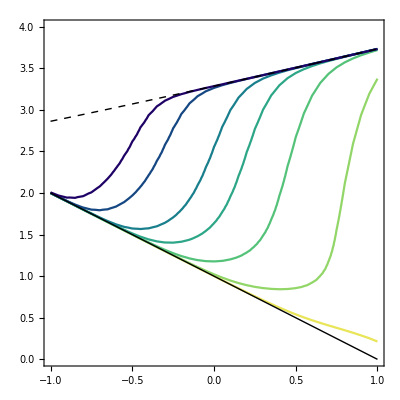

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}],Plot[(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thick,Dashed]],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

## Supplementary figure 3 - panel C

```mathematica
tmaxB = {20,25,30,35,40,50,60};
NE0 =0;
NH0 = 1;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Flatten[{Table[i,{i,0,0.1,0.01}],Table[i,{i,0.15,4,0.07}]}];
TabKH =10^-{7};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatD=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

### Optimal strategies

```mathematica
OptTest=ResultatD[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{{{{-1.,0.,2},{-1.,0.01,2},{-1.,0.02,2},{-1.,0.03,2},{-1.,0.04,2},{-1.,0.05,2},{-1.,0.06,-3},{-1.,0.07,-3},{-1.,0.08,-3},{-1.,0.09,-3},{-1.,0.1,-3},2725,{1.,3.3,1},{1.,3.37,1},{1.,3.44,1},{1.,3.51,1},{1.,3.58,1},{1.,3.65,1},{1.,3.72,1},{1.,3.79,1},{1.,3.86,1},{1.,3.93,1},{1.,4.,1}},5,{1}}}
 |  |  |  |

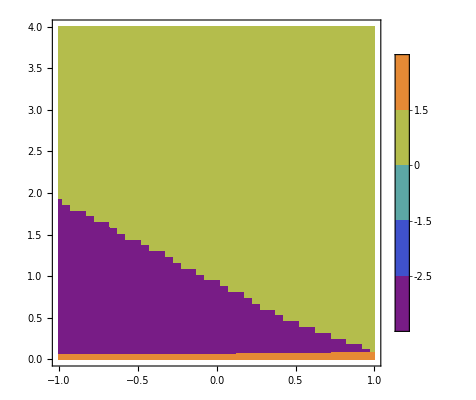
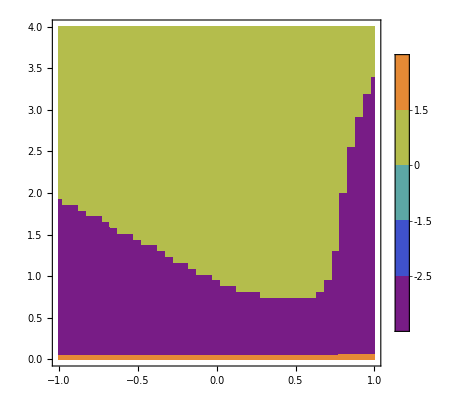
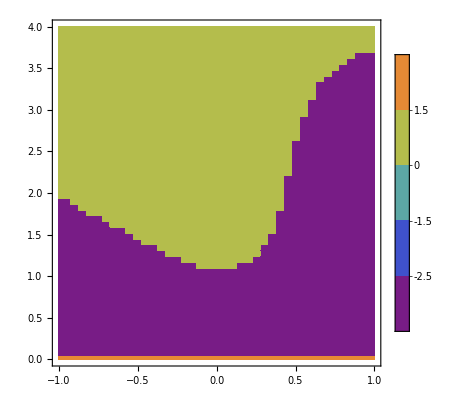
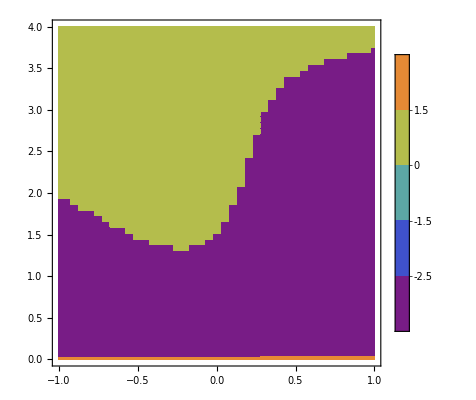
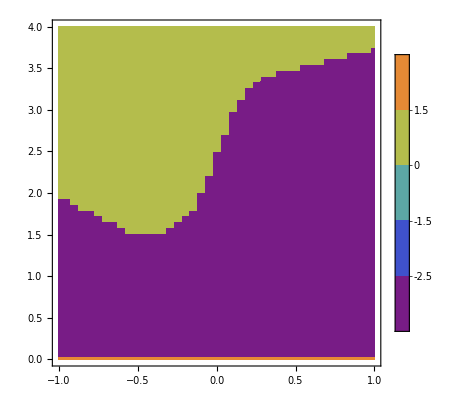
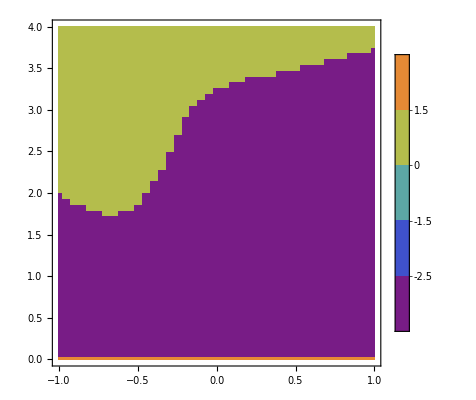
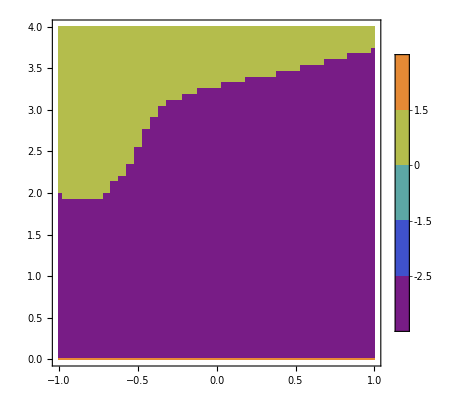

```mathematica
Table[ListContourPlot[dataOptTest⟦1,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

### Contour Plot

```mathematica
listcolor=Reverse[Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[tmaxB])}]]
```

{RGBColor[0.914809, 0.897673, 0.350652],RGBColor[0.6208947142857143, 0.8482312857142857, 0.39989485714285716],RGBColor[0.3987782857142857, 0.7844317142857143, 0.45559771428571433],RGBColor[0.24151514285714284, 0.699388, 0.505396],RGBColor[0.14216071428571428, 0.5862125714285714, 0.5369255714285714],RGBColor[0.09378314285714286, 0.43570714285714285, 0.5372898571428572],RGBColor[0.08943771428571429, 0.24098401142857143, 0.49412457142857147],RGBColor[0.122103, 0.00901808, 0.39826]}

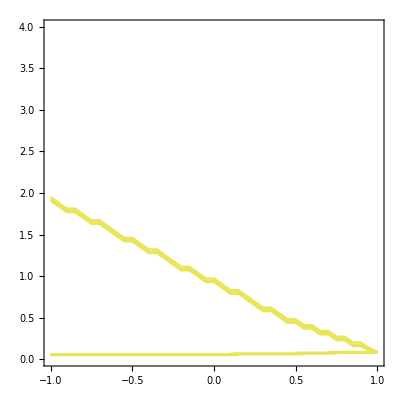
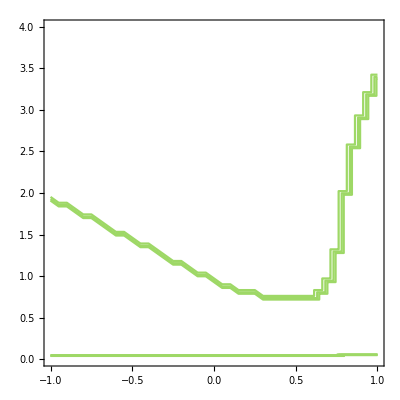
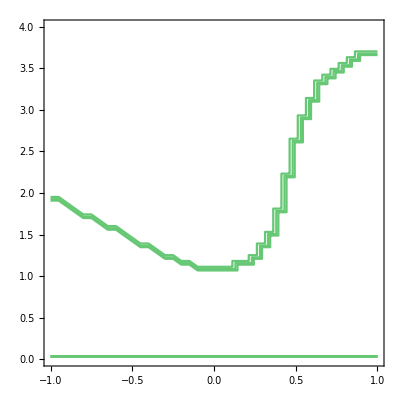
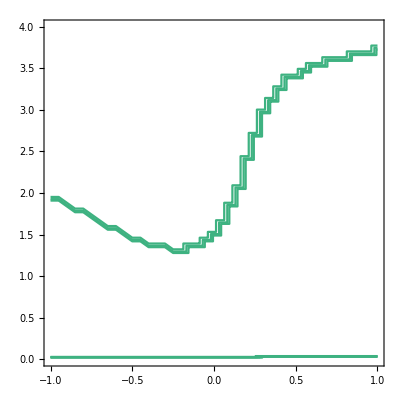
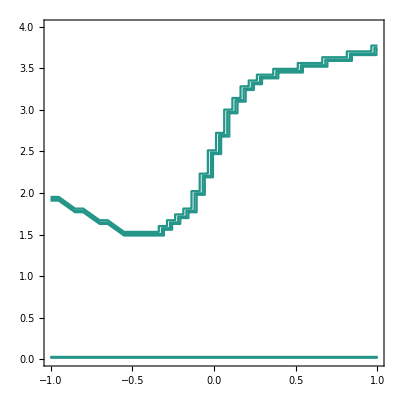
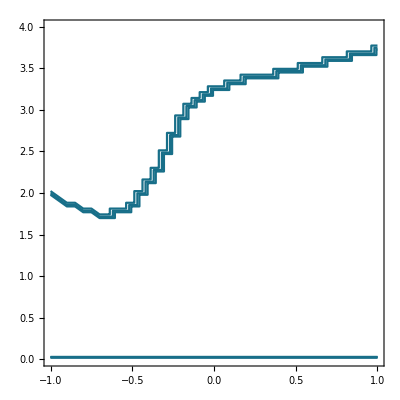
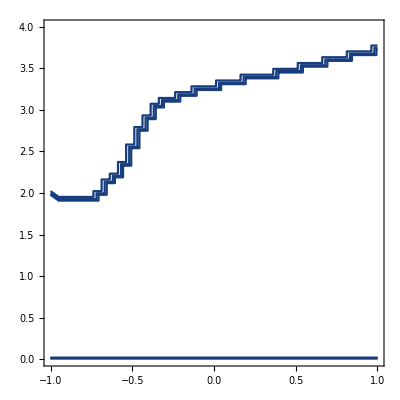

```mathematica
Table[ListContourPlot[dataOptTest[[1,itmax]],ContourShading->None,Contours->{-2.5,-1.5,0,1.5,2.5},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}]
```

```mathematica
SensiRH=ResultatD[[1,3]];
```

```mathematica
SensiMH=ResultatD[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiMH[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

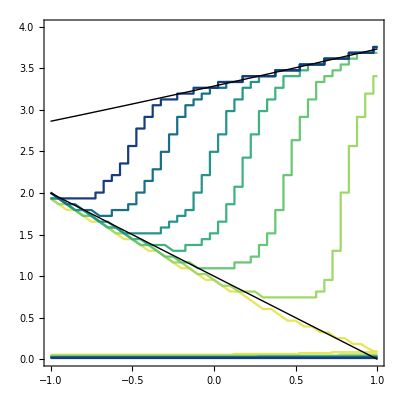

```mathematica
Show[Table[ListContourPlot[dataOptTest[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}],Plot[(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thick]],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]]
```

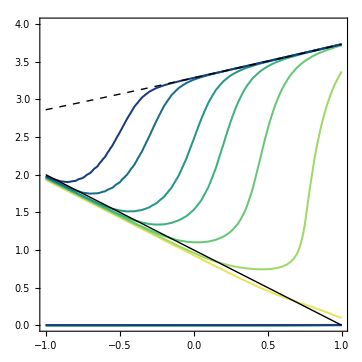

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{itmax,1,Length[tmaxB]}],Plot[(8+rho)/6-(-34-10 rho-rho^2)/(6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3))+1/6 (206+75 rho+15 rho^2+rho^3+3 √3 √(116-140 rho-69 rho^2-14 rho^3-rho^4))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thick,Dashed]],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```